```mathematica
spherePoint[dim_]:=Table[RandomVariate[NormalDistribution[]],dim]//Normalize;
feasibilifySimplex[vertices_]:=Module[{m=#-Last[vertices]&/@Most[vertices],lastVertexNewCoords,multipliers},
lastVertexNewCoords=-Last[vertices].Inverse[m];
multipliers=Append[If[#>=0,1,-1]&/@lastVertexNewCoords,If[Total[lastVertexNewCoords]<=1,1,-1]];
vertices*multipliers
];
generateSimplexWithZeroInside[dim_]:=feasibilifySimplex[Table[spherePoint[dim],dim+1]];
```

```mathematica
plotF3D[A_]:=Module[{directedEdges,F},
directedEdges=Join[Subsets[A,{2}],Subsets[A,{2}][[All,{2,1}]]];
F=RegionIntersection[BoundaryDiscretizeGraphics[HalfSpace[#[[1]]-#[[2]],#[[1]]],PlotRange->10]&/@directedEdges];
Show[
Graphics3D[{Opacity[0.7],F}],
Graphics3D[{{Opacity[0.7],EdgeForm[Thick],Simplex[A]},{Opacity[0.5],Sphere[]}}]
]
];
```

```mathematica
makeF3D[A_,range_]:=With[{directedEdges=Join[Subsets[A,{2}],Subsets[A,{2}][[All,{2,1}]]]},
RegionIntersection[BoundaryDiscretizeGraphics[HalfSpace[#[[1]]-#[[2]],#[[1]]],PlotRange->range]&/@directedEdges]
];
```

```mathematica
volF3D[A_]:=Module[{directedEdges=Join[Subsets[A,{2}],Subsets[A,{2}][[All,{2,1}]]],F3,F5,F10,vol},
F3=RegionIntersection[BoundaryDiscretizeGraphics[HalfSpace[#[[1]]-#[[2]],#[[1]]],PlotRange->3]&/@directedEdges];
F5=RegionIntersection[BoundaryDiscretizeGraphics[HalfSpace[#[[1]]-#[[2]],#[[1]]],PlotRange->5]&/@directedEdges];
F10=RegionIntersection[BoundaryDiscretizeGraphics[HalfSpace[#[[1]]-#[[2]],#[[1]]],PlotRange->10]&/@directedEdges];
vol=Max[Volume/@{F3,F5,F10}];
Clear[F3,F5,F10];
vol
];
```

```mathematica
minVertexPairDist[A_]:=Min[Norm[#[[1]]-#[[2]]]&/@Subsets[A,{2}]];
```

```mathematica
A=Append[Sqrt[1+1/3]#-3^(-3/2)(Sqrt[3+1]-1)*{1,1,1}&/@{{1,0,0},{0,1,0},{0,0,1}},-Sqrt[1/3]*{1,1,1}];
plotF3D[A]
```

-Graphics3D-

```mathematica
(*A=Table[spherePoint[3],3+1];*)
A=generateSimplexWithZeroInside[3];
volF3D[A]/Volume[Simplex[A]]
plotF3D[A]
```

8.67057

-Graphics3D-

```mathematica
eps=0.05;
A=Normalize/@{{1,0,eps},{0,1,-eps},{-1,0,eps},{0,-1,-eps}};
Print["Vol(A)=",ToString[Volume[Simplex[A]]],"\nVol(F)=",ToString[volF3D[A]]]
plotF3D[A]
```

Vol(A)=0.0664174
Vol(F)=13.4837

-Graphics3D-

```mathematica
eps=0.1;
A=Normalize/@{{1,0,0},{0,1,0},{-1,-1,eps},{-1,-1,-eps}};
volF3D[A]/Volume[Simplex[A]]
plotF3D[A]
```

6.

-Graphics3D-

```mathematica
as=Table[generateSimplexWithZeroInside[3],100];
avols=Volume[Simplex[#]]&/@as;
fvols={};
For[i=1,i<=Length[as],i++,AppendTo[fvols,volF3D[as[[i]]]]];
```

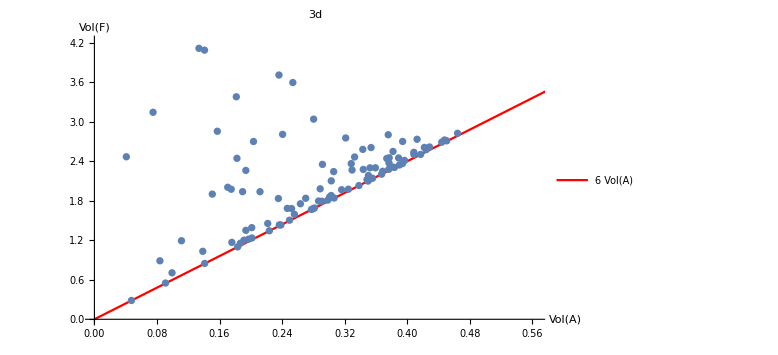

```mathematica
Show[
Plot[6x,{x,0,1},PlotStyle->Red,PlotLegends->{"6 Vol(A)"},PlotRange->{{0,Max[avols]+0.1},{0,Max[fvols]+0.1}},ImageSize->Large,AxesLabel->{"Vol(A)","Vol(F)"},PlotLabel->"3d"],
ListPlot[{avols,fvols}//Transpose]
]
```

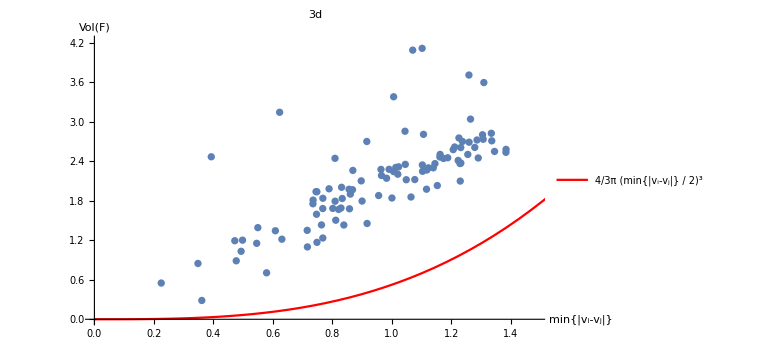

```mathematica
minVertexPairDists=minVertexPairDist/@as;
Show[
Plot[4π (x/2)^3/3,{x,0,2},PlotStyle->Red,PlotLegends->{"4/3π (min{|v_i-v_j|} / 2)^3"},PlotRange->{{0,Max[minVertexPairDists]+0.1},{0,Max[fvols]+0.1}},ImageSize->Large,AxesLabel->{"min{|v_i-v_j|}","Vol(F)"},PlotLabel->"3d"],
ListPlot[{minVertexPairDists,fvols}//Transpose]
]
```

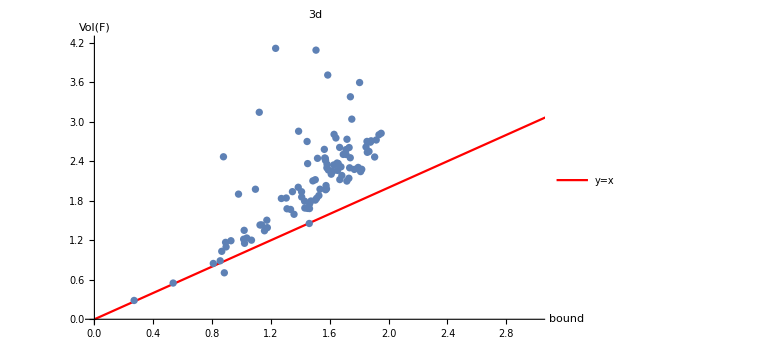

```mathematica
bound[A_]:=Module[
{indexedA,pairs,i,j,newEdges,gram},
indexedA=Transpose[{A,Table[i,{i,Length[A]}]}];
pairs={Norm[#[[1,1]]-#[[2,1]]],{#[[1,2]],#[[2,2]]}}&/@Subsets[indexedA,{2}];
{i,j}=Last[First[MinimalBy[pairs,First]]];
newEdges=Delete[(#-A[[i]])&/@A,{{i},{j}}];
gram=Table[newEdges[[k]].newEdges[[l]],{k,Length[newEdges]},{l,Length[newEdges]}];
Sqrt[Det[gram]]*Norm[A[[i]]-A[[j]]]/Sqrt[1+Norm[A[[i]]-A[[j]]]^2]
];
bounds=bound/@as;
Show[
Plot[x,{x,0,5},PlotStyle->Red,PlotLegends->{"y=x"},PlotRange->{{0,3},{0,Max[fvols]+0.1}},ImageSize->Large,AxesLabel->{"bound","Vol(F)"},PlotLabel->"3d"],
ListPlot[{bounds,fvols}//Transpose]
]
```